```mathematica
QuantumGroupsPath="c:\\scott\\projects\\svn-checkouts\\QuantumGroups\\trunk\\package\\";
AppendTo[$Path, QuantumGroupsPath];
<<QuantumGroups`
```

Loading QuantumGroups` version 2.0
Read more at http://katlas.math.toronto.edu/wiki/QuantumGroups

```mathematica
AppendTo[$ContextPath,"QuantumGroups`LittelmannPaths`Internals`"];
```

### Drawing pictures of weights and paths

```mathematica
WeightsGraphic[Subscript[A, 2]][weights:{___},opts___]:=ListPlot[({{-1/2, 1/2}, {√3/2, √3/2}}).#&/@weights,opts,PlotRange->All,PlotStyle->PointSize[0.02],AspectRatio->1,DisplayFunction->(#&)]
```

```mathematica
LittelmannPathGraphic[lp:LittelmannPath[Γ_][_]]:=WeightsGraphic[Γ][QuantumGroups`LittelmannPaths`Internals`LittelmannPathVertices[lp],PlotStyle->Hue[0.6],PlotJoined->True]
```

```mathematica
PositiveWeylChamberGraphic[Subscript[A, 2]][cutoff_]:=Graphics[Line[({{-1/2, 1/2}, {√3/2, √3/2}}).#&/@{{cutoff,0},{0,0},{0,cutoff}}]]
```

```mathematica
SimpleRootsGraphic[Subscript[A, 2]]:=Graphics[{PointSize[0.02]}~Join~(Point[({{-1/2, 1/2}, {√3/2, √3/2}}).#]&/@SimpleRoots[Subscript[A, 2]])]
```

```mathematica
RootsGraphic[Subscript[A, 2]]:=Graphics[{PointSize[0.02]}~Join~(Point[({{-1/2, 1/2}, {√3/2, √3/2}}).#]&/@(PositiveRoots[Subscript[A, 2]]~Join~(-PositiveRoots[Subscript[A, 2]])))]
```

```mathematica
DisplayLittelmannPathGraphic[lp_]:=DisplayLittelmannPathGraphic[lp,Max[Plus@@Abs[#]&/@QuantumGroups`LittelmannPaths`Internals`LittelmannPathVertices[lp]]+1]
DisplayLittelmannPathGraphic[lp:LittelmannPath[Γ_][_],cutoff_]:=
Show[PositiveWeylChamberGraphic[Subscript[A, 2]][cutoff],RootsGraphic[Subscript[A, 2]],LittelmannPathGraphic[lp],DisplayFunction->$DisplayFunction,AspectRatio->1]
```

### Examples

```mathematica
lp=LittelmannPath[Subscript[A, 2]][{{0,2},{2,0},{0,2},{1,-1}}];
```

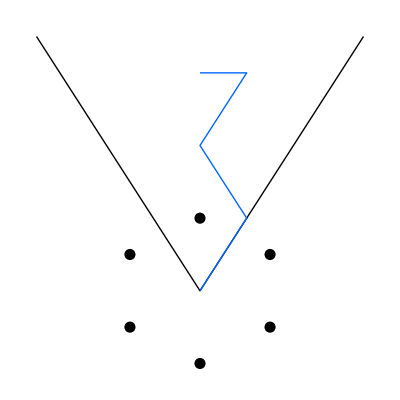

```mathematica
DisplayLittelmannPathGraphic[lp]
```

```mathematica
DisplayLittelmannPathGraphic[LowerLittelmannPath[lp,1,3]]
```

⁃Graphics⁃

```mathematica
Show@@Table[DisplayLittelmannPathGraphic[LowerLittelmannPath[lp,1,k]],{k,0,3}]
```

⁃Graphics⁃

```mathematica
lp=LittelmannPath[Subscript[A, 2]][{{1,1}}];
```

```mathematica
DisplayLittelmannPathGraphic[lp]
```

⁃Graphics⁃

```mathematica
DisplayLittelmannPathGraphic/@LittelmannPathLowerings[lp]
```

{⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃}

```mathematica
Show[%]
```

⁃Graphics⁃